# Properties of Hyperbolic Trig Functions.

#### DEFINITIONS: (Expressions are similar to Sin and Cos, except without the ⅈ's.) Sinh[x] = (ⅇ^x- ⅇ^-x)/2 Cosh[x] =(ⅇ^x + ⅇ^-x)/2

#### Therefore, the inverse can be written as (Similar to Sin and Cos, except without the ⅈ's.) ⅇ^x = Cosh[x] + Sinh[x] ⅇ^-x = Cosh[x] - Sinh[x]

#### Values at the origin (Similar to Sin and Cos.) Sinh[0]=0 Cosh[0]=1

#### Derivatives (Similar to Sin and Cos, but without the sign change.) ∂_x Sinh[x]=Cosh[x] ∂_x Cosh[x]=Sinh[x]

```mathematica
D[Sinh[x], x]
```

Cosh[x]

```mathematica
D[Cosh[x], x]
```

Sinh[x]

#### Identity (Similar to Sin and Cos, but with a minus sign.) Cosh[x]^2-Sinh[x]^2=1

```mathematica
Simplify[Cosh[x]^2-Sinh[x]^2]
```

1

#### Plots of Sinh, Cosh, and Tanh

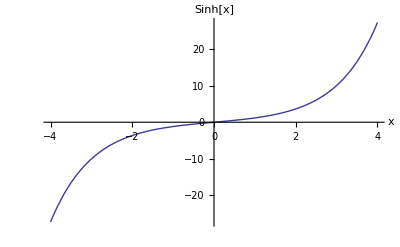

```mathematica
Plot[Sinh[x],{x,-4,4},AxesLabel->{"x","Sinh[x]"},BaseStyle->{FontSize->18},PlotStyle->Thick]
```

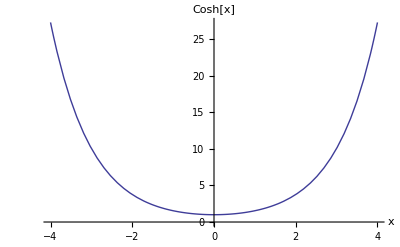

```mathematica
Plot[Cosh[x],{x,-4,4},AxesLabel->{"x","Cosh[x]"},BaseStyle->{FontSize->18},PlotStyle->Thick]
```

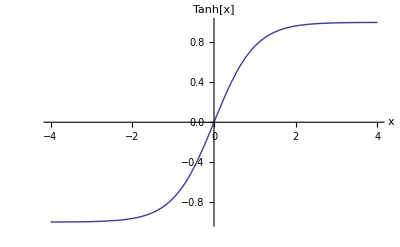

```mathematica
Plot[Tanh[x],{x,-4,4},AxesLabel->{"x","Tanh[x]"},BaseStyle->{FontSize->18},PlotStyle->Thick]
```